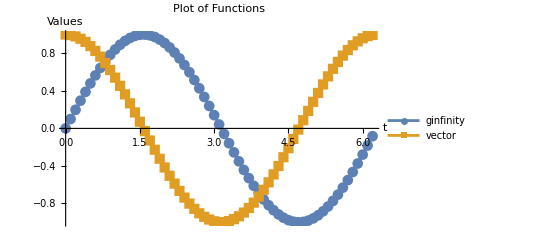

```mathematica
(*Example data:Replace with your actual arrays*)timeinterval=Range[0,2 Pi,0.1];
ginfinity=Sin[timeinterval];
vector=Cos[timeinterval];  (*Replace with your actual vector data*)

(*Plot both ginfinity and vector on the same graph using ListLinePlot*)
ListLinePlot[{Transpose[{timeinterval,ginfinity}],Transpose[{timeinterval,vector}]},PlotMarkers->Automatic,AxesLabel->{"t","Values"},PlotLabel->"Plot of Functions",PlotLegends->{"ginfinity","vector"}]
```